# Density Matrix Simulation

## Theory

## Test ρ=|+><+|, σ=|0> ⅇ^-iρt σ = ⅇ^(-i(|+><+|)t) |0>

-Graphics--Graphics-

0.75

0.25

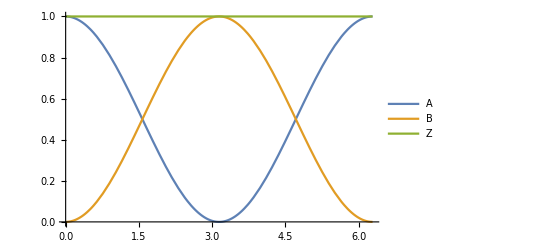

```mathematica
A=(Abs[(Exp[- I*t]+1)/2])^2;
B=(Abs[(Exp[- I*t]-1)/2])^2;
Z=A+B;
A/.t->Pi/3.0
B/.t->Pi/3.0
Plot[{ A,B,Z},{t,0,2*Pi}, PlotLegends->{"A","B","Z"}]
```